# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

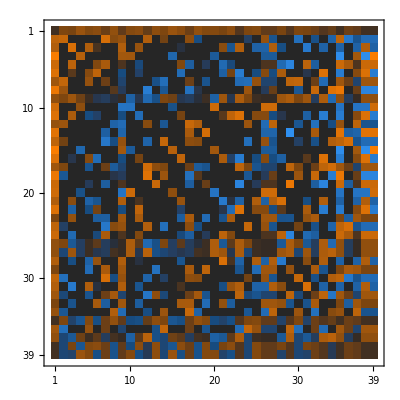

(1/4 √(1-1/(√5)) | 0 | 0 | 1/2 (1+1/(√5))^(1/4) | 1/2 √(1/10 (5+√5)) | 0 | 1/(2 5^(1/4)) | 0 | 1/4 √(1+1/(√5)) | 1/2 (1-1/(√5))^(1/4) | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 1/2 (1+1/(√5))^(1/4) | 0 | 1/(2 5^(1/4)) | 0 | 1/2 √(1/10 (5+√5)) | 1/2 (1-1/(√5))^(1/4) | 0 | 0 | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | 1/4 √(1+1/(√5)) | 1/4 √(1+1/(√5)) | 0 | √(1/8-1/(8 √5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/8-1/(8 √5)) | 0 | 1/4 √(1-1/(√5)) | 1/(2 5^(1/4)) | 1/4 √(1+1/(√5)) | 1/4 √(1-1/(√5)) | 1/4 √(1-1/(√5))
√(1/10 (5+√5)) | 0 | 0 | 0 | 0 | 0 | 5^(1/4)/(√2) | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 0 | 0 | 0 | 0 |  | 0 | 0 | √(1/10 (5+√5)) |  |  |  | 
1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | -1/(√2) | 0 | -1/(√2) | 1/(√2) | -1/(√2)
1/2 (1+√5) | 0 | 0 | (1+1/(√5))^(1/4)/(√2) | 0 | 0 | 0 | 0 | 1/2 (-1+√5) |  | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-1-√5) | 0 | 1/2 (-1+√5) | 1/2 (-1-√5) | 1/2 (1+√5)
√(1/2+1/(√5)) | 0 | 0 | 0 | 0 | 0 | 1/5^(1/4) | 0 | √(1/2-1/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5^(1/4) | 0 | -√(1-2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | √(1/2-1/(√5)) | √(1/2-1/(√5)) | 0 | -√(1+2/(√5)) | 0 | 0 | -1/5^(1/4) | 0 | 0 | √(1/2+1/(√5)) | 1/5^(1/4) | √(1/2-1/(√5)) | √(1/2+1/(√5)) | √(1/2+1/(√5))
(√(3+√5))/2 | 0 | 0 | 0 | (√(3-√5))/2 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 √(3+√5) | 0 |  | (√(3-√5))/2 |  | 0 | 0 | 0 | 0 | 0 | (√(3+√5))/2 | 0 | -1/2 √(3+√5) | 0 | (√(3-√5))/2 | (√(3+√5))/2 | -1/2 √(3+√5)
1/2 √(1+1/(√5)) | 0 | 0 | 0 |  | 0 | 1/(2 5^(1/4)) | 0 | -1/2 √(1-1/(√5)) | 0 | 0 | 0 |  | 0 | 0 | 0 | 1/(2 5^(1/4)) | 0 |  | 0 | 0 | 0 |  | 0 |  | -1/2 √(1-1/(√5)) | -1/2 √(1-1/(√5)) | 0 | √(1/10 (5+√5)) | 0 | 0 | 1/(2 5^(1/4)) |  | 0 | 1/2 √(1+1/(√5)) | 1/(2 5^(1/4)) | -1/2 √(1-1/(√5)) | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5))
√(1+2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(1-2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(1-2/(√5)) | √(1-2/(√5)) | 0 | 0 | 0 | 0 | (√2)/5^(1/4) | 0 | 0 | √(1+2/(√5)) | 0 | √(1-2/(√5)) | -√(1+2/(√5)) | -√(1+2/(√5))
1/40 (5+√5)^(3/2) | 0 | 0 |  | 1/2 √(1-2/(√5)) | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1/2-1/(√5)) | -(1/8+1/(4 √5))^(1/4) | 0 | 0 |  | 0 |  | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1-2/(√5)) | -(1/8+1/(4 √5))^(1/4) | 0 | 0 | √(1/4+1/(2 √5)) | 0 | 1/2 √(1-2/(√5)) | 1/2 √(1/2-1/(√5)) | 1/2 √(1/2-1/(√5)) | 0 | √(1/4+1/(2 √5)) | 0 | 0 | -1/(2 5^(1/4)) | √(1/4+1/(2 √5)) | 0 | 1/40 (5+√5)^(3/2) | -1/(2 5^(1/4)) | 1/2 √(1/2-1/(√5)) | 1/40 (5+√5)^(3/2) | 1/40 (5+√5)^(3/2)
1 | 0 | 0 | (1/2-1/(√5))^(1/4) | 0 | 0 | 0 | 0 | -1 | -(1/2+1/(√5))^(1/4) | 0 | 0 | 0 | 0 | -(1/2-1/(√5))^(1/4) | 0 | 0 | 0 | 0 | (1/2+1/(√5))^(1/4) | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 1
(√(3+√5))/2 | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(3+√5))/2 | 0 | (√(3-√5))/2 | (√(3-√5))/2 |  | 0 | 0 | 0 | 0 | 0 | -1/2 √(3+√5) | 0 | -1/2 √(3+√5) | 0 | (√(3-√5))/2 | (√(3+√5))/2 | -1/2 √(3+√5)
 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√2)/5^(1/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | √(1/10 (5+√5)) | 0 | 0 | 0 | 0 |  | 0 | 0 |  | 0 | √(1/10 (5+√5)) |  | 
√(1+1/(√5)) | 0 | 0 | 0 | 0 | 0 | -1/5^(1/4) | 0 | -√(1-1/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5^(1/4) | 0 | √(2-2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | -√(1-1/(√5)) | -√(1-1/(√5)) | 0 | -√(2+2/(√5)) | 0 | 0 | 1/5^(1/4) | 0 | 0 | √(1+1/(√5)) | -1/5^(1/4) | -√(1-1/(√5)) | √(1+1/(√5)) | √(1+1/(√5))
√(1/10 (5+√5)) | 0 | 0 | 0 | 0 | 0 |  | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 0 | 0 | 0 | 0 |  | 0 | 0 | √(1/10 (5+√5)) | 5^(1/4)/(√2) |  |  | 
1/2 (1+√5) | 0 | 0 |  | 0 | 0 | 0 | 0 | 1/2 (-1+√5) |  | 0 | 0 | 0 | 0 | (1+1/(√5))^(1/4)/(√2) | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-1-√5) | 0 | 1/2 (-1+√5) | 1/2 (-1-√5) | 1/2 (1+√5)
(√(3+√5))/2 | 0 | 0 | 0 | (√(3-√5))/2 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 √(3+√5) | 0 |  | (√(3-√5))/2 |  | 0 | 0 | 0 | 0 | 0 | (√(3+√5))/2 | 0 | -1/2 √(3+√5) | 0 | (√(3-√5))/2 | (√(3+√5))/2 | -1/2 √(3+√5)
1/2 √(1+1/(√5)) | 0 | 0 | 0 |  | 0 | 1/(2 5^(1/4)) | 0 | -1/2 √(1-1/(√5)) | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 1/(2 5^(1/4)) | 0 |  | 0 | 0 | 0 | √(1/10 (5+√5)) | 0 |  | -1/2 √(1-1/(√5)) | -1/2 √(1-1/(√5)) | 0 | √(1/10 (5+√5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/10 (5+√5)) | 0 | 1/2 √(1+1/(√5)) | 1/(2 5^(1/4)) | -1/2 √(1-1/(√5)) | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5))
√(1+2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(1-2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(1-2/(√5)) | √(1-2/(√5)) | 0 | 0 | 0 | 0 | (√2)/5^(1/4) | 0 | 0 | √(1+2/(√5)) | 0 | √(1-2/(√5)) | -√(1+2/(√5)) | -√(1+2/(√5))
√(1/2+1/(√5)) | 0 | 0 | 0 | -√(1-2/(√5)) | 0 | -1/5^(1/4) | 0 | √(1/2-1/(√5)) | 0 | 0 | 0 | (√2)/5^(1/4) | 0 | 0 | 0 | -1/5^(1/4) | 0 | √(1-2/(√5)) | 0 | 0 | 0 | -√(1+2/(√5)) | 0 | -√(1-2/(√5)) | √(1/2-1/(√5)) | √(1/2-1/(√5)) | 0 | √(1+2/(√5)) | 0 | 0 | -1/5^(1/4) | -√(1+2/(√5)) | 0 | √(1/2+1/(√5)) | -1/5^(1/4) | √(1/2-1/(√5)) | √(1/2+1/(√5)) | √(1/2+1/(√5))
1 | 0 | 0 | -(1/2-1/(√5))^(1/4) | 0 | 0 | 0 | 0 | -1 | (1/2+1/(√5))^(1/4) | 0 | 0 | 0 | 0 | (1/2-1/(√5))^(1/4) | 0 | 0 | 0 | 0 | -(1/2+1/(√5))^(1/4) | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 1
1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | -1/(√2) | 1/(√2) | -1/(√2)
(√(3+√5))/2 | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(3+√5))/2 | 0 | (√(3-√5))/2 | (√(3-√5))/2 |  | 0 | 0 | 0 | 0 | 0 | -1/2 √(3+√5) | 0 | -1/2 √(3+√5) | 0 | (√(3-√5))/2 | (√(3+√5))/2 | -1/2 √(3+√5)
1/2 √(1-1/(√5)) | 0 | 0 | 0 | 0 | 0 | -1/5^(1/4) | 0 | 1/2 √(1+1/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5^(1/4) | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5)) | 0 |  | 0 | 0 | 1/5^(1/4) | 0 | 0 | 1/2 √(1-1/(√5)) | -1/5^(1/4) | 1/2 √(1+1/(√5)) | 1/2 √(1-1/(√5)) | 1/2 √(1-1/(√5))
√(1/10 (5+√5)) | 0 | 0 | 0 | 0 | 0 |  | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 0 | 0 | 0 | 0 |  | 0 | 0 | √(1/10 (5+√5)) | 5^(1/4)/(√2) |  |  | 
√(1/2+1/(√5)) | 0 | 0 | 0 | 0 | 0 | 1/5^(1/4) | 0 | √(1/2-1/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5^(1/4) | 0 | -√(1-2/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | √(1/2-1/(√5)) | √(1/2-1/(√5)) | 0 | -√(1+2/(√5)) | 0 | 0 | -1/5^(1/4) | 0 | 0 | √(1/2+1/(√5)) | 1/5^(1/4) | √(1/2-1/(√5)) | √(1/2+1/(√5)) | √(1/2+1/(√5))
1/40 (5+√5)^(3/2) | 0 | 0 |  | 1/2 √(1-2/(√5)) | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1/2-1/(√5)) | (1/8+1/(4 √5))^(1/4) | 0 | 0 |  | 0 |  | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1-2/(√5)) | (1/8+1/(4 √5))^(1/4) | 0 | 0 | √(1/4+1/(2 √5)) | 0 | 1/2 √(1-2/(√5)) | 1/2 √(1/2-1/(√5)) | 1/2 √(1/2-1/(√5)) | 0 | √(1/4+1/(2 √5)) | 0 | 0 | -1/(2 5^(1/4)) | √(1/4+1/(2 √5)) | 0 | 1/40 (5+√5)^(3/2) | -1/(2 5^(1/4)) | 1/2 √(1/2-1/(√5)) | 1/40 (5+√5)^(3/2) | 1/40 (5+√5)^(3/2)
1/40 (5+√5)^(3/2) | 0 | 0 |  | 1/2 √(1-2/(√5)) | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1/2-1/(√5)) | (1/8+1/(4 √5))^(1/4) | 0 | 0 |  | 0 |  | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1-2/(√5)) | (1/8+1/(4 √5))^(1/4) | 0 | 0 | √(1/4+1/(2 √5)) | 0 | 1/2 √(1-2/(√5)) | 1/2 √(1/2-1/(√5)) | 1/2 √(1/2-1/(√5)) | 0 | √(1/4+1/(2 √5)) | 0 | 0 | -1/(2 5^(1/4)) | √(1/4+1/(2 √5)) | 0 | 1/40 (5+√5)^(3/2) | -1/(2 5^(1/4)) | 1/2 √(1/2-1/(√5)) | 1/40 (5+√5)^(3/2) | 1/40 (5+√5)^(3/2)
1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2) | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | -1/(√2) | 1/(√2) | -1/(√2)
1/2 √(1-1/(√5)) | 0 | 0 | 0 |  | 0 | 1/5^(1/4) | 0 | 1/2 √(1+1/(√5)) | 0 | 0 | 0 |  | 0 | 0 | 0 | 1/5^(1/4) | 0 | √(1/10 (5+√5)) | 0 | 0 | 0 |  | 0 |  | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5)) | 0 |  | 0 | 0 | 1/5^(1/4) |  | 0 | 1/2 √(1-1/(√5)) | 1/5^(1/4) | 1/2 √(1+1/(√5)) | 1/2 √(1-1/(√5)) | 1/2 √(1-1/(√5))
√(1/10 (5+√5)) | 0 | 0 | 0 | 0 | 0 | 5^(1/4)/(√2) | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 0 | 0 | 0 | 0 |  | 0 | 0 | √(1/10 (5+√5)) |  |  |  | 
1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | -1/(√2) | 0 | -1/(√2) | 1/(√2) | -1/(√2)
1/2 √(1+1/(√5)) | 0 | 0 | 0 |  | 0 | 1/(2 5^(1/4)) | 0 | -1/2 √(1-1/(√5)) | 0 | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 0 | 0 | 1/(2 5^(1/4)) | 0 |  | 0 | 0 | 0 | √(1/10 (5+√5)) | 0 |  | -1/2 √(1-1/(√5)) | -1/2 √(1-1/(√5)) | 0 | √(1/10 (5+√5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/10 (5+√5)) | 0 | 1/2 √(1+1/(√5)) | 1/(2 5^(1/4)) | -1/2 √(1-1/(√5)) | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5))
1/2 √(1-1/(√5)) | 0 | 0 | 0 | 0 | 0 | -1/5^(1/4) | 0 | 1/2 √(1+1/(√5)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5^(1/4) | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5)) | 0 |  | 0 | 0 | 1/5^(1/4) | 0 | 0 | 1/2 √(1-1/(√5)) | -1/5^(1/4) | 1/2 √(1+1/(√5)) | 1/2 √(1-1/(√5)) | 1/2 √(1-1/(√5))
 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√2)/5^(1/4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | √(1/10 (5+√5)) | 0 | 0 | 0 | 0 |  | 0 | 0 |  | 0 | √(1/10 (5+√5)) |  | 
1/4 √(1-1/(√5)) | 0 | 0 | -1/2 (1+1/(√5))^(1/4) | 1/2 √(1/10 (5+√5)) | 0 | 1/(2 5^(1/4)) | 0 | 1/4 √(1+1/(√5)) | -1/2 (1-1/(√5))^(1/4) | 0 | 0 | 1/(√2 5^(1/4)) | 0 | -1/2 (1+1/(√5))^(1/4) | 0 | 1/(2 5^(1/4)) | 0 | 1/2 √(1/10 (5+√5)) | -1/2 (1-1/(√5))^(1/4) | 0 | 0 | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | 1/4 √(1+1/(√5)) | 1/4 √(1+1/(√5)) | 0 | √(1/8-1/(8 √5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/8-1/(8 √5)) | 0 | 1/4 √(1-1/(√5)) | 1/(2 5^(1/4)) | 1/4 √(1+1/(√5)) | 1/4 √(1-1/(√5)) | 1/4 √(1-1/(√5))
1/2 √(1+1/(√5)) | 0 | 0 | 0 |  | 0 | 1/(2 5^(1/4)) | 0 | -1/2 √(1-1/(√5)) | 0 | 0 | 0 |  | 0 | 0 | 0 | 1/(2 5^(1/4)) | 0 |  | 0 | 0 | 0 |  | 0 |  | -1/2 √(1-1/(√5)) | -1/2 √(1-1/(√5)) | 0 | √(1/10 (5+√5)) | 0 | 0 | 1/(2 5^(1/4)) |  | 0 | 1/2 √(1+1/(√5)) | 1/(2 5^(1/4)) | -1/2 √(1-1/(√5)) | 1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5))
1/40 (5+√5)^(3/2) | 0 | 0 |  | 1/2 √(1-2/(√5)) | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1/2-1/(√5)) | -(1/8+1/(4 √5))^(1/4) | 0 | 0 |  | 0 |  | 0 | -1/(2 5^(1/4)) | 0 | 1/2 √(1-2/(√5)) | -(1/8+1/(4 √5))^(1/4) | 0 | 0 | √(1/4+1/(2 √5)) | 0 | 1/2 √(1-2/(√5)) | 1/2 √(1/2-1/(√5)) | 1/2 √(1/2-1/(√5)) | 0 | √(1/4+1/(2 √5)) | 0 | 0 | -1/(2 5^(1/4)) | √(1/4+1/(2 √5)) | 0 | 1/40 (5+√5)^(3/2) | -1/(2 5^(1/4)) | 1/2 √(1/2-1/(√5)) | 1/40 (5+√5)^(3/2) | 1/40 (5+√5)^(3/2)
1/4 √(1-1/(√5)) | 0 | 0 | -1/2 (1+1/(√5))^(1/4) | 1/2 √(1/10 (5+√5)) | 0 | 1/(2 5^(1/4)) | 0 | 1/4 √(1+1/(√5)) | -1/2 (1-1/(√5))^(1/4) | 0 | 0 | 1/(√2 5^(1/4)) | 0 | -1/2 (1+1/(√5))^(1/4) | 0 | 1/(2 5^(1/4)) | 0 | 1/2 √(1/10 (5+√5)) | -1/2 (1-1/(√5))^(1/4) | 0 | 0 | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | 1/4 √(1+1/(√5)) | 1/4 √(1+1/(√5)) | 0 | √(1/8-1/(8 √5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/8-1/(8 √5)) | 0 | 1/4 √(1-1/(√5)) | 1/(2 5^(1/4)) | 1/4 √(1+1/(√5)) | 1/4 √(1-1/(√5)) | 1/4 √(1-1/(√5))
1/4 √(1-1/(√5)) | 0 | 0 | 1/2 (1+1/(√5))^(1/4) | 1/2 √(1/10 (5+√5)) | 0 | 1/(2 5^(1/4)) | 0 | 1/4 √(1+1/(√5)) | 1/2 (1-1/(√5))^(1/4) | 0 | 0 | 1/(√2 5^(1/4)) | 0 | 1/2 (1+1/(√5))^(1/4) | 0 | 1/(2 5^(1/4)) | 0 | 1/2 √(1/10 (5+√5)) | 1/2 (1-1/(√5))^(1/4) | 0 | 0 | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | 1/4 √(1+1/(√5)) | 1/4 √(1+1/(√5)) | 0 | √(1/8-1/(8 √5)) | 0 | 0 | 1/(2 5^(1/4)) | √(1/8-1/(8 √5)) | 0 | 1/4 √(1-1/(√5)) | 1/(2 5^(1/4)) | 1/4 √(1+1/(√5)) | 1/4 √(1-1/(√5)) | 1/4 √(1-1/(√5)))

Time:   0.878141

```mathematica
(* Calculate Boundaries in TIM^2/Z_2 and Pull back to TIM^2 *)
Module[
{md,s,boundaries, defects, x, pullbacks},
md=ModularDataFoldZ2OrbifoldMinimal[];
s=md["S"];

(* Calculate boundaries *)
boundaries = #/Sqrt[#[[1]]] & /@ s//Transpose;
boundaries//MatrixPlot//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify;

(* It looks like there are 3 Z_2's in there in a Z_2^2, 
   so which one is the inverse? 
(probably the diagonal one) *)
x = Transpose[defects][[-1]];

(*The pullback is going to be *)
pullbacks = (# + x * #)/2&/@ boundaries // FullSimplify;
pullbacks // MatrixForm//Echo;
]//Time
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md,20] //Time;
traces = mb["defects"] // ToRoots//Time;
qdim = Transpose[traces][[1]];
r=Length@qdim;
traces //Transpose // MatrixForm
```

Time:   0.086401

Time:   1.93894

Time:   0.239237

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 0 | 1-√5 | 1-√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 0 | 1+√5 | 1+√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

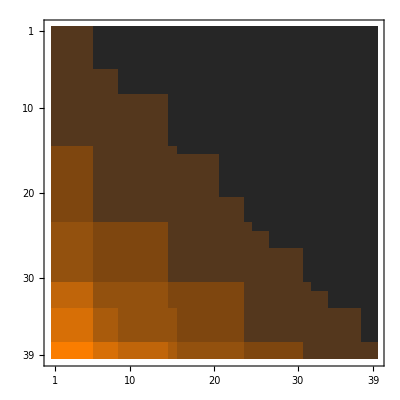
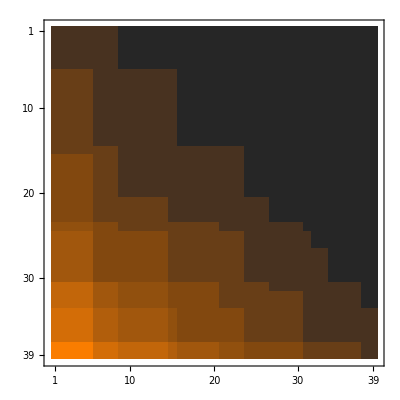
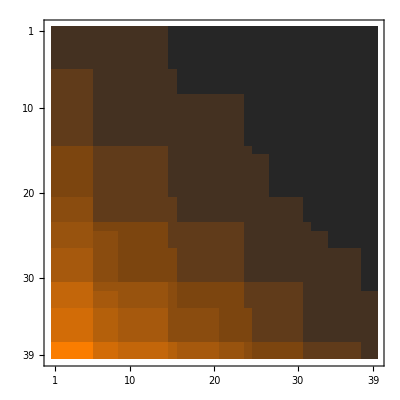
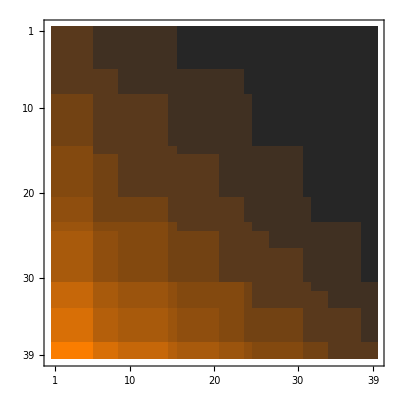
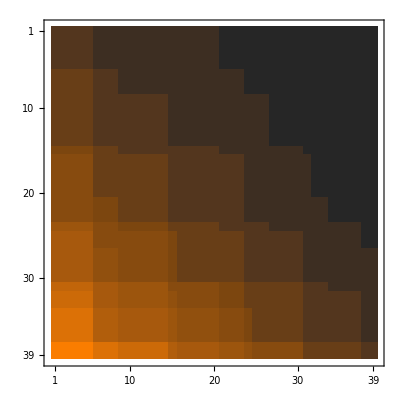
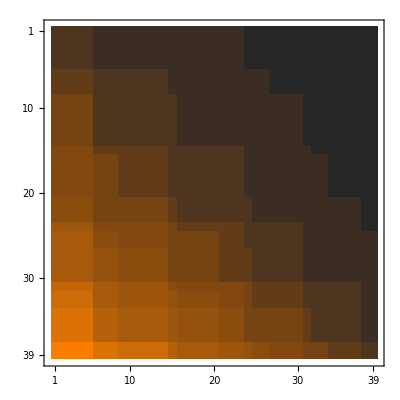
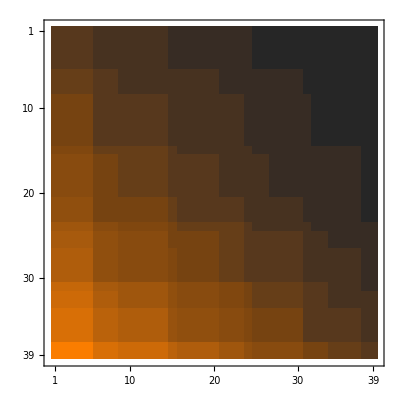
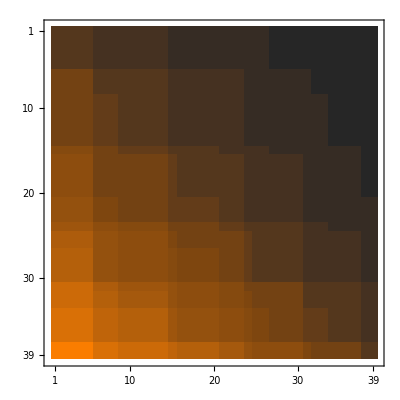
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
B=Array[Floor@N[qdim[[#1]]qdim[[#2]]/qdim[[#3]]] &, {r,r,r}];
MatrixPlot /@B
```

```mathematica
traces
```

{{1,1,0,-1,-1,2,0,1,1,0,-2,0,2,0,2,-1,-1,0,-1,-1,1,1,1,1,2,0,2,-1,-1,0,1,1,2,1,1,1,1,1,1},{1,-1,0,1,-1,0,0,1,-1,0,0,0,0,0,0,1,-1,0,-1,1,-1,1,1,-1,0,0,0,-1,1,0,-1,1,0,-1,1,1,-1,-1,1},{1,1,-2,1,1,2,-2,1,1,-2,2,-2,2,-2,2,1,1,-2,1,1,1,1,1,1,2,-2,2,1,1,-2,1,1,2,1,1,1,1,1,1},{1,1,2,1,1,2,2,1,1,2,2,2,2,2,2,1,1,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,1,1,1,1,1},{1,-1,0,-1,1,0,0,1,-1,0,0,0,0,0,0,-1,1,0,1,-1,-1,1,1,-1,0,0,0,1,-1,0,-1,1,0,-1,1,1,-1,-1,1},{√2,√2,√2,0,0,0,-√2,-√2,-√2,√2,0,-√2,2 √2,√2,0,0,0,√2,0,0,-√2,-√2,√2,√2,0,-√2,-2 √2,0,0,-√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,√2,-√2,0,0,0,√2,-√2,-√2,-√2,0,√2,2 √2,-√2,0,0,0,-√2,0,0,-√2,-√2,√2,√2,0,√2,-2 √2,0,0,√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,-√2,0,0,0,0,0,-√2,√2,0,0,0,0,0,0,0,0,0,0,0,√2,-√2,√2,-√2,0,0,0,0,0,0,-√2,√2,0,-√2,√2,-√2,√2,√2,-√2},{1/2 (1+√5),1/2 (1+√5),√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,-√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (1-√5),1/2 (-1+√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1,1-√5,1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1,1-√5,1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1/2 (1+√5),1/2 (1+√5),1+√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1,-1+√5,1/2 (1-√5),1/2 (1-√5),-1-√5,1,-1,1,-1+√5,1-√5,1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-1,1,1/2 (1+√5),1/2 (1+√5),-1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (1-√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{2,2,0,0,0,-4,0,2,2,0,0,0,4,0,-4,0,0,0,0,0,2,2,2,2,-4,0,4,0,0,0,2,2,-4,2,2,2,2,2,2},{√(3+√5),√(3+√5),-√(3-√5),0,0,-√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,-√(3+√5),√2,-√(3-√5),0,0,0,√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3-√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),-√(3+√5),0,0,√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,-√(3-√5),√2,√(3-√5),0,0,0,√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3+√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3+√5),0,0,√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,√(3-√5),√2,-√(3-√5),0,0,0,-√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3+√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3-√5),0,0,-√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,√(3+√5),√2,√(3-√5),0,0,0,-√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3-√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),-√(3+√5),0,0,0,0,0,√(3-√5),-√(3-√5),0,0,0,0,0,0,0,0,0,0,0,-√(3-√5),√(3-√5),-√(3-√5),√(3-√5),0,0,0,0,0,0,-√(3+√5),√(3+√5),0,√(3-√5),-√(3-√5),-√(3+√5),√(3+√5),√(3+√5),-√(3+√5)},{1/2 (3+√5),1/2 (3+√5),0,1/2 (-3+√5),1/2 (-3+√5),-2,0,1/2 (3-√5),1/2 (3-√5),0,2,0,-2,0,3-√5,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (-3+√5),1/2 (-3+√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,0,-2,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),-2,3-√5,1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,-2,3-√5,3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,1/2 (3+√5),1/2 (3+√5),3+√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),-2,-3+√5,1/2 (3-√5),1/2 (3-√5),-3-√5,-2,2,-2,-3+√5,3-√5,1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,2,-2,1/2 (3+√5),1/2 (3+√5),-3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1+√5,1+√5,0,0,0,-2,0,1-√5,1-√5,0,0,0,2,0,-2+2 √5,0,0,0,0,0,1-√5,1-√5,1-√5,1-√5,-2-2 √5,0,2,0,0,0,1+√5,1+√5,-2,1-√5,1-√5,1+√5,1+√5,1+√5,1+√5},{√(7+3 √5),√(7+3 √5),√2,0,0,0,√(7-3 √5),-√(7-3 √5),-√(7-3 √5),-√(7+3 √5),0,-√2,-2 √2,-√(7-3 √5),0,0,0,√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,-√2,2 √2,0,0,√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(7+3 √5),√(7+3 √5),-√2,0,0,0,-√(7-3 √5),-√(7-3 √5),-√(7-3 √5),√(7+3 √5),0,√2,-2 √2,√(7-3 √5),0,0,0,-√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,√2,2 √2,0,0,-√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(2 (5+√5)),-√(2 (5+√5)),0,-√(5-√5),√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),√(5+√5),0,-√(5-√5),√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,-√(5+√5),√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),-√(2 (5+√5)),0,√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),-√(5+√5),0,√(5-√5),-√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,√(5+√5),-√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,√(5-√5),√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),√(5+√5),0,-√(5-√5),-√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,-√(5+√5),-√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,-√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),-√(5+√5),0,√(5-√5),√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,√(5+√5),√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{3+√5,3+√5,0,0,0,4,0,3-√5,3-√5,0,0,0,-4,0,-6+2 √5,0,0,0,0,0,3-√5,3-√5,3-√5,3-√5,-6-2 √5,0,-4,0,0,0,3+√5,3+√5,4,3-√5,3-√5,3+√5,3+√5,3+√5,3+√5},{2 √(5+√5),-2 √(5+√5),0,0,0,0,0,-2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,-2 √(5-√5),2 √(5-√5),2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,2 √(5+√5),-2 √(5+√5),0,2 √(5-√5),-2 √(5-√5),-2 √(5+√5),2 √(5+√5),-2 √(5+√5),2 √(5+√5)},{2 √(5+√5),2 √(5+√5),0,0,0,0,0,-2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,2 √(5-√5),2 √(5-√5),2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,-2 √(5+√5),-2 √(5+√5),0,-2 √(5-√5),-2 √(5-√5),-2 √(5+√5),-2 √(5+√5),2 √(5+√5),2 √(5+√5)},{2 √(5+2 √5),2 √(5+2 √5),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),2 √(5+2 √5),0,√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5))},{2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),2 √(2 (5+2 √5))}}

```mathematica
AA=Select[traces//Transpose,#[[4]]!=2&];
vals=Union[Flatten[AA]];
field=ToNumberField[vals,All];
A=AA/. Thread[vals->field];
x=Array[x,r];
F= [A];
```

LinearSolve::sqmat1: The matrix {«1»} is not square, so a factorization will not be saved.

```mathematica
{i,j}={38,4};
b=A[[All,i]]*A[[All,j]];
M=B[[i,j]];
F[b]//Chop//Rationalize//Time
x/.#& /@Solve[Thread[A . x == b]~Join~Thread[ 0<= x <= M],x,Integers]
```

Time:   0.000319

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
A//FullSimplify//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5))

```mathematica
PolynomialCoefficients[x_]:=PolynomialCoefficients[x]=CoefficientList[MinimalPolynomial[x,y],y];
NumericalValue[x_]  := Round[N[x,40]*10^30];
ParseEntry[i_,j_]:=Module[
{coefficients = PolynomialCoefficients[AA[[i,j]]]},
{i,j,Length[coefficients]-1, coefficients, NumericalValue[AA[[i,j]]]}
];
Aexport=Flatten[Array[ParseEntry,Dimensions[AA]],1];//Time
Export[ModuleDirectory<>"fusion/in/A.txt", Aexport]
```

Time:   0.011402

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt